# Bell Violation

## Hong-Ou-Mandel CSCH Inequality - Entangled State & Squeezed State

Valerio Paper 1

Emlyn Graham

Department of Quantum Science

19/08/2018

## Squeezed State - 3 Measurement (N, X, P)

#### Eigenfunctions of Quantum Harmonic Oscillator

```mathematica
ϕ[n_,x_]=FullSimplify[((π^(1/4)*Sqrt[n!*2^n])^(-1))*HermiteH[n,x]*Exp[-(x^2)/2]]
```

(ⅇ^(-x^2/2) HermiteH[n,x])/(π^(1/4) √(2^n n!))

#### Probabilities and expectation values

```mathematica
PN[1]=1/2;
PN[1]=1/2;
PNN[1,1]=0;
PNN[0,0]=0;
PNN[1,0]=1/2;
PNN[0,1]=1/2
```

1/2

```mathematica
PNX[1,1,z_]=0.5*Integrate[ϕ[0,x]^2,{x,-z,z},Assumptions->z∈Reals];
PNX[1,0,z_]=0.5*(Integrate[ϕ[0,x]^2,{x,-Infinity,-z},Assumptions->z∈Reals]+Integrate[ϕ[0,x]^2,{x,z,Infinity},Assumptions->z∈Reals]);
PNX[0,0,z_]=0.5*(Integrate[ϕ[1,x]^2,{x,-Infinity,-z},Assumptions->z∈Reals]+Integrate[ϕ[1,x]^2,{x,z,Infinity},Assumptions->z∈Reals]);
PNX[0,1,z_]=0.5*Integrate[ϕ[1,x]^2,{x,-z,z},Assumptions->z∈Reals]
```

0.5 (-(2 ⅇ^(-z^2) z)/(√π)+Erf[z])

```mathematica
PXN[1,1,z_]=PNX[1,1,z];
PXN[0,0,z_]=PNX[0,0,z];
PXN[1,0,z_]=PNX[0,1,z];
PXN[0,1,z_]=PNX[1,0,z]
```

0.5 Erfc[z]

```mathematica
PNP[1,1,z_]=PNX[1,1,z];
PNP[1,0,z_]=PNX[1,0,z];
PNP[0,1,z_]=PNX[0,1,z];
PNP[0,0,z_]=PNX[0,0,z];
PPN[1,1,z_]=PXN[1,1,z];
PPN[1,0,z_]=PXN[1,0,z];
PPN[0,1,z_]=PXN[0,1,z];
PPN[0,0,z_]=PXN[0,0,z]
```

0.5 ((2 ⅇ^(-z^2) z)/(√π)+Erfc[z])

```mathematica
PXXIntegrand[x_,y_] = (ϕ[0,x]^2)*(ϕ[1,y]^2)+(ϕ[0,y]^2)*(ϕ[1,x]^2)+2*ϕ[0,x]*ϕ[1,x]*ϕ[0,y]*ϕ[1,y];
PXX[1,1,z_]=0.5*Integrate[PXXIntegrand[x,y],{x,-z,z},{y,-z,z},Assumptions->z∈Reals];
PXX[1,0,z_]=0.5*Integrate[PXXIntegrand[x,y],{x,-z,z},{y,-Infinity,-z},Assumptions->z∈Reals]+0.5*Integrate[PXXIntegrand[x,y],{x,-z,z},{y,z,Infinity},Assumptions->z∈Reals];
PXX[0,1,z_]=PXX[1,0,z];
PXX[0,0,z_]=1-PXX[1,1,z]-PXX[1,0,z]-PXX[0,1,z];
PPP[1,1,z_]=PXX[1,1,z];
PPP[1,0,z_]=PXX[1,0,z];
PPP[0,1,z_]=PXX[0,1,z];
PPP[0,0,z_]=PXX[0,0,z]
```

1-1. Erf[z] (-(2 ⅇ^(-z^2) z)/(√π)+Erf[z])-2. (Erf[z] Erfc[z]+(ⅇ^(-z^2) (z-2 z Erfc[z]))/(√π))

```mathematica
PXPIntegrand[x_,p_]=Abs[ϕ[0,x]^2+ϕ[1,x]^2]*Abs[ϕ[0,p]^2+ϕ[1,p]^2];
PXP[1,1,z_]=0.25*Integrate[PXPIntegrand[x,p],{x,-z,z},{p,-z,z},Assumptions->z∈Reals&&z>0];
PXP[1,0,z_]=0.25*Integrate[PXPIntegrand[x,p],{x,-z,z},{p,-Infinity,-z},Assumptions->z∈Reals&&z>0]+0.25*Integrate[PXPIntegrand[x,p],{x,-z,z},{p,z,Infinity},Assumptions->z∈Reals&&z>0];
PXP[0,1,z_]=0.25*Integrate[PXPIntegrand[x,p],{x,-Infinity,-z},{p,-z,z},Assumptions->z∈Reals&&z>0]+0.25*Integrate[PXPIntegrand[x,p],{x,z,Infinity},{p,-z,z},Assumptions->z∈Reals&&z>0];
PXP[0,0,z_]=1-PXP[1,1,z]-PXP[1,0,z]-PXP[0,1,z];
PPX[1,1,z_]=PXP[1,1,z];
PPX[1,0,z_]=PXP[0,1,z];
PPX[0,1,z_]=PXP[1,0,z];
PPX[0,0,z_]=PXP[0,0,z]
```

1-0.31831 ⅇ^(-2 z^2) (-z+ⅇ^(z^2) √π Erf[z])^2-0.63662 ⅇ^(-2 z^2) (-z+ⅇ^(z^2) √π Erf[z]) (z+ⅇ^(z^2) √π Erfc[z])

```mathematica
S[z_]=FullSimplify[PN[1]+PN[1]-PNN[1,1]-2*PNX[1,1,z]-2*PNP[1,1,z]-PXX[1,1,z]+2*PXP[1,1,z]]
```

1.+0.63662 ⅇ^(-2 z^2) z^2+(-2.-1.12838 ⅇ^(-z^2) z+1. Erf[z]) Erf[z]

```mathematica
NMinimize[S[z],z]
```

{-0.243442,{z→1.07426}}

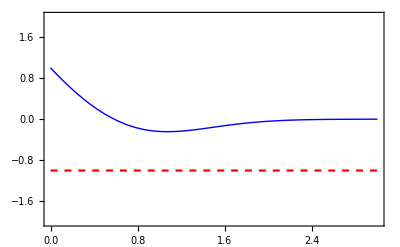

```mathematica
Show[Plot[S[z],{z,0,3},Frame->True,PlotRange->{{0,3},{-2,2}},AxesOrigin->{0,3},PlotStyle->{Thin,Blue}, PlotPoints->50, MaxRecursion->2],Plot[-1,{z,0,3},Frame->True,PlotRange->{{0,3},{-2,2}},AxesOrigin->{0,3},PlotStyle->{Dashed,Red}]]
```

```mathematica
output[z_] = {{PNN[0,0],PNN[0,1],PNX[0,0,z],PNX[0,1,z],PNP[0,0,z],PNP[0,1,z]},{PNN[1,0],PNN[1,1],PNX[1,0,z],PNX[1,1,z],PNP[1,0,z],PNP[1,1,z]},{PXN[0,0,z],PXN[0,1,z],PXX[0,0,z],PXX[0,1,z],PXP[0,0,z],PXP[0,1,z]},{PXN[1,0,z],PXN[1,1,z],PXX[1,0,z],PXX[1,1,z],PXP[1,0,z],PXP[1,1,z]},{PPN[0,0,z],PPN[0,1,z],PPX[0,0,z],PPX[0,1,z],PPP[0,0,z],PPP[0,1,z]},{PPN[1,0,z],PPN[1,1,z],PPX[1,0,z],PPX[1,1,z],PPP[1,0,z],PPP[1,1,z]}}
```

{{0,1/2,0.5 ((2 ⅇ^(-z^2) z)/(√π)+Erfc[z]),0.5 (-(2 ⅇ^(-z^2) z)/(√π)+Erf[z]),0.5 ((2 ⅇ^(-z^2) z)/(√π)+Erfc[z]),0.5 (-(2 ⅇ^(-z^2) z)/(√π)+Erf[z])},{1/2,0,0.5 Erfc[z],0.5 Erf[z],0.5 Erfc[z],0.5 Erf[z]},{0.5 ((2 ⅇ^(-z^2) z)/(√π)+Erfc[z]),0.5 Erfc[z],1-1. Erf[z] (-(2 ⅇ^(-z^2) z)/(√π)+Erf[z])-2. (Erf[z] Erfc[z]+(ⅇ^(-z^2) (z-2 z Erfc[z]))/(√π)),1. (Erf[z] Erfc[z]+(ⅇ^(-z^2) (z-2 z Erfc[z]))/(√π)),1-0.31831 ⅇ^(-2 z^2) (-z+ⅇ^(z^2) √π Erf[z])^2-0.63662 ⅇ^(-2 z^2) (-z+ⅇ^(z^2) √π Erf[z]) (z+ⅇ^(z^2) √π Erfc[z]),0.31831 ⅇ^(-2 z^2) (-z+ⅇ^(z^2) √π Erf[z]) (z+ⅇ^(z^2) √π Erfc[z])},{0.5 (-(2 ⅇ^(-z^2) z)/(√π)+Erf[z]),0.5 Erf[z],1. (Erf[z] Erfc[z]+(ⅇ^(-z^2) (z-2 z Erfc[z]))/(√π)),1. Erf[z] (-(2 ⅇ^(-z^2) z)/(√π)+Erf[z]),0.31831 ⅇ^(-2 z^2) (-z+ⅇ^(z^2) √π Erf[z]) (z+ⅇ^(z^2) √π Erfc[z]),0.31831 ⅇ^(-2 z^2) (-z+ⅇ^(z^2) √π Erf[z])^2},{0.5 ((2 ⅇ^(-z^2) z)/(√π)+Erfc[z]),0.5 Erfc[z],1-0.31831 ⅇ^(-2 z^2) (-z+ⅇ^(z^2) √π Erf[z])^2-0.63662 ⅇ^(-2 z^2) (-z+ⅇ^(z^2) √π Erf[z]) (z+ⅇ^(z^2) √π Erfc[z]),0.31831 ⅇ^(-2 z^2) (-z+ⅇ^(z^2) √π Erf[z]) (z+ⅇ^(z^2) √π Erfc[z]),1-1. Erf[z] (-(2 ⅇ^(-z^2) z)/(√π)+Erf[z])-2. (Erf[z] Erfc[z]+(ⅇ^(-z^2) (z-2 z Erfc[z]))/(√π)),1. (Erf[z] Erfc[z]+(ⅇ^(-z^2) (z-2 z Erfc[z]))/(√π))},{0.5 (-(2 ⅇ^(-z^2) z)/(√π)+Erf[z]),0.5 Erf[z],0.31831 ⅇ^(-2 z^2) (-z+ⅇ^(z^2) √π Erf[z]) (z+ⅇ^(z^2) √π Erfc[z]),0.31831 ⅇ^(-2 z^2) (-z+ⅇ^(z^2) √π Erf[z])^2,1. (Erf[z] Erfc[z]+(ⅇ^(-z^2) (z-2 z Erfc[z]))/(√π)),1. Erf[z] (-(2 ⅇ^(-z^2) z)/(√π)+Erf[z])}}

```mathematica
Total[output[1.]]
```

9.

```mathematica
rangelist = Range[0.01,1.0,0.01]
```

{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.}

```mathematica
outlist = Map[output,rangelist];
```

```mathematica
Export["C:\\Users\\emlyn\\Google Drive\\Undergrad 5th year\\Semester 2\\Quantum Computing\\singletfcn.mat",output[z]]
```

BinaryWrite::nocoerce: 0.5 (1.12838 2.71828^(-1. z^2) z+Erfc[z]) cannot be coerced to the specified format.

C:\Users\emlyn\Google Drive\Undergrad 5th year\Semester 2\Quantum Computing\singletfcn.mat

```mathematica
output[z]//MatrixForm
```

(0 | 1/2 | 0.5 ((2 ⅇ^(-z^2) z)/(√π)+Erfc[z]) | 0.5 (-(2 ⅇ^(-z^2) z)/(√π)+Erf[z]) | 0.5 ((2 ⅇ^(-z^2) z)/(√π)+Erfc[z]) | 0.5 (-(2 ⅇ^(-z^2) z)/(√π)+Erf[z])
1/2 | 0 | 0.5 Erfc[z] | 0.5 Erf[z] | 0.5 Erfc[z] | 0.5 Erf[z]
0.5 ((2 ⅇ^(-z^2) z)/(√π)+Erfc[z]) | 0.5 Erfc[z] | 1-1. Erf[z] (-(2 ⅇ^(-z^2) z)/(√π)+Erf[z])-2. (Erf[z] Erfc[z]+(ⅇ^(-z^2) (z-2 z Erfc[z]))/(√π)) | 1. (Erf[z] Erfc[z]+(ⅇ^(-z^2) (z-2 z Erfc[z]))/(√π)) | 1-0.31831 ⅇ^(-2 z^2) (-z+ⅇ^(z^2) √π Erf[z])^2-0.63662 ⅇ^(-2 z^2) (-z+ⅇ^(z^2) √π Erf[z]) (z+ⅇ^(z^2) √π Erfc[z]) | 0.31831 ⅇ^(-2 z^2) (-z+ⅇ^(z^2) √π Erf[z]) (z+ⅇ^(z^2) √π Erfc[z])
0.5 (-(2 ⅇ^(-z^2) z)/(√π)+Erf[z]) | 0.5 Erf[z] | 1. (Erf[z] Erfc[z]+(ⅇ^(-z^2) (z-2 z Erfc[z]))/(√π)) | 1. Erf[z] (-(2 ⅇ^(-z^2) z)/(√π)+Erf[z]) | 0.31831 ⅇ^(-2 z^2) (-z+ⅇ^(z^2) √π Erf[z]) (z+ⅇ^(z^2) √π Erfc[z]) | 0.31831 ⅇ^(-2 z^2) (-z+ⅇ^(z^2) √π Erf[z])^2
0.5 ((2 ⅇ^(-z^2) z)/(√π)+Erfc[z]) | 0.5 Erfc[z] | 1-0.31831 ⅇ^(-2 z^2) (-z+ⅇ^(z^2) √π Erf[z])^2-0.63662 ⅇ^(-2 z^2) (-z+ⅇ^(z^2) √π Erf[z]) (z+ⅇ^(z^2) √π Erfc[z]) | 0.31831 ⅇ^(-2 z^2) (-z+ⅇ^(z^2) √π Erf[z]) (z+ⅇ^(z^2) √π Erfc[z]) | 1-1. Erf[z] (-(2 ⅇ^(-z^2) z)/(√π)+Erf[z])-2. (Erf[z] Erfc[z]+(ⅇ^(-z^2) (z-2 z Erfc[z]))/(√π)) | 1. (Erf[z] Erfc[z]+(ⅇ^(-z^2) (z-2 z Erfc[z]))/(√π))
0.5 (-(2 ⅇ^(-z^2) z)/(√π)+Erf[z]) | 0.5 Erf[z] | 0.31831 ⅇ^(-2 z^2) (-z+ⅇ^(z^2) √π Erf[z]) (z+ⅇ^(z^2) √π Erfc[z]) | 0.31831 ⅇ^(-2 z^2) (-z+ⅇ^(z^2) √π Erf[z])^2 | 1. (Erf[z] Erfc[z]+(ⅇ^(-z^2) (z-2 z Erfc[z]))/(√π)) | 1. Erf[z] (-(2 ⅇ^(-z^2) z)/(√π)+Erf[z]))

```mathematica
<<ToMatlab`
output[z]// ToMatlab
```

[0,(1/2),0.5E0.*(2.*exp(1).^((-1).*z.^2).*pi.^(-1/2).*z+erfc(z)), ...
  0.5E0.*((-2).*exp(1).^((-1).*z.^2).*pi.^(-1/2).*z+erf(z)),0.5E0.*( ...
  2.*exp(1).^((-1).*z.^2).*pi.^(-1/2).*z+erfc(z)),0.5E0.*((-2).*exp( ...
  1).^((-1).*z.^2).*pi.^(-1/2).*z+erf(z));(1/2),0,0.5E0.*erfc(z), ...
  0.5E0.*erf(z),0.5E0.*erfc(z),0.5E0.*erf(z);0.5E0.*(2.*exp(1).^(( ...
  -1).*z.^2).*pi.^(-1/2).*z+erfc(z)),0.5E0.*erfc(z),1+(-0.1E1).*erf( ...
  z).*((-2).*exp(1).^((-1).*z.^2).*pi.^(-1/2).*z+erf(z))+(-0.2E1).*( ...
  erf(z).*erfc(z)+exp(1).^((-1).*z.^2).*pi.^(-1/2).*(z+(-2).*z.* ...
  erfc(z))),0.1E1.*(erf(z).*erfc(z)+exp(1).^((-1).*z.^2).*pi.^(-1/2) ...
  .*(z+(-2).*z.*erfc(z))),1+(-0.31831E0).*exp(1).^((-2).*z.^2).*(( ...
  -1).*z+exp(1).^(z.^2).*pi.^(1/2).*erf(z)).^2+(-0.63662E0).*exp(1) ...
  .^((-2).*z.^2).*((-1).*z+exp(1).^(z.^2).*pi.^(1/2).*erf(z)).*(z+ ...
  exp(1).^(z.^2).*pi.^(1/2).*erfc(z)),0.31831E0.*exp(1).^((-2).* ...
  z.^2).*((-1).*z+exp(1).^(z.^2).*pi.^(1/2).*erf(z)).*(z+exp(1).^( ...
  z.^2).*pi.^(1/2).*erfc(z));0.5E0.*((-2).*exp(1).^((-1).*z.^2).* ...
  pi.^(-1/2).*z+erf(z)),0.5E0.*erf(z),0.1E1.*(erf(z).*erfc(z)+exp(1) ...
  .^((-1).*z.^2).*pi.^(-1/2).*(z+(-2).*z.*erfc(z))),0.1E1.*erf(z).*( ...
  (-2).*exp(1).^((-1).*z.^2).*pi.^(-1/2).*z+erf(z)),0.31831E0.*exp( ...
  1).^((-2).*z.^2).*((-1).*z+exp(1).^(z.^2).*pi.^(1/2).*erf(z)).*(z+ ...
  exp(1).^(z.^2).*pi.^(1/2).*erfc(z)),0.31831E0.*exp(1).^((-2).* ...
  z.^2).*((-1).*z+exp(1).^(z.^2).*pi.^(1/2).*erf(z)).^2;0.5E0.*(2.* ...
  exp(1).^((-1).*z.^2).*pi.^(-1/2).*z+erfc(z)),0.5E0.*erfc(z),1+( ...
  -0.31831E0).*exp(1).^((-2).*z.^2).*((-1).*z+exp(1).^(z.^2).*pi.^( ...
  1/2).*erf(z)).^2+(-0.63662E0).*exp(1).^((-2).*z.^2).*((-1).*z+exp( ...
  1).^(z.^2).*pi.^(1/2).*erf(z)).*(z+exp(1).^(z.^2).*pi.^(1/2).* ...
  erfc(z)),0.31831E0.*exp(1).^((-2).*z.^2).*((-1).*z+exp(1).^(z.^2) ...
  .*pi.^(1/2).*erf(z)).*(z+exp(1).^(z.^2).*pi.^(1/2).*erfc(z)),1+( ...
  -0.1E1).*erf(z).*((-2).*exp(1).^((-1).*z.^2).*pi.^(-1/2).*z+erf(z) ...
  )+(-0.2E1).*(erf(z).*erfc(z)+exp(1).^((-1).*z.^2).*pi.^(-1/2).*(z+ ...
  (-2).*z.*erfc(z))),0.1E1.*(erf(z).*erfc(z)+exp(1).^((-1).*z.^2).* ...
  pi.^(-1/2).*(z+(-2).*z.*erfc(z)));0.5E0.*((-2).*exp(1).^((-1).* ...
  z.^2).*pi.^(-1/2).*z+erf(z)),0.5E0.*erf(z),0.31831E0.*exp(1).^(( ...
  -2).*z.^2).*((-1).*z+exp(1).^(z.^2).*pi.^(1/2).*erf(z)).*(z+exp(1) ...
  .^(z.^2).*pi.^(1/2).*erfc(z)),0.31831E0.*exp(1).^((-2).*z.^2).*(( ...
  -1).*z+exp(1).^(z.^2).*pi.^(1/2).*erf(z)).^2,0.1E1.*(erf(z).*erfc( ...
  z)+exp(1).^((-1).*z.^2).*pi.^(-1/2).*(z+(-2).*z.*erfc(z))),0.1E1.* ...
  erf(z).*((-2).*exp(1).^((-1).*z.^2).*pi.^(-1/2).*z+erf(z))];